```mathematica
qq = BinaryReadList["/Users/am10485/PycharmProjects/LoopEquations/plots/EulerPhi/Probs.10000000.np","Integer64"];
```

```mathematica
Dimensions[qq]
```

{10000000}

```mathematica
fitdata=
Block[{ SQ,W, digits=16, M = Length[qq]},
SQ = Accumulate[qq];
W = N[1-SQ/SQ[[-1]],digits];
Transpose[{N[Range[M],digits]/M,W}]
];
```

```mathematica
Dwn[a_, n_] := a[[#]]& /@ Range[1,Length[a],n];
```

```mathematica
testdata = Dwn[fitdata,100];
```

```mathematica
Dimensions[testdata]
```

{100000,2}

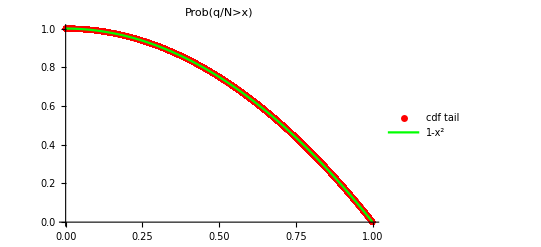

```mathematica
Show[
ListPlot[testdata, PlotStyle->{Red, PointSize[0.01]},
PlotLegends->{"cdf tail"}],
Plot[1-x^2,{x,0,1},PlotStyle->{Green, Thick},
PlotLegends->{1-x^2},PlotRange->All],
PlotLabel->Prob[q/N> x ]
]
```